# Implement Petri Net

Pumeng Lyu

(Jofre Espigule-Pons)

In my project, I am going to write a package to visualize a mathematical modeling language for the description of distributed systems called Petri net. Petri net is a set of discrete event dynamic system. Let’s further explore the usefulness of Petri net and how I try to visualize and make analysis on it step by step.

## What consists of a Petri net?

A Petri net includes places, transitions and arcs. Arcs must go from a place to a transition or vice versa, which makes a Petri net a directed bipartite graph and the nodes represent transitions (events that may occur to cause change in states, marked by square) and places (conditions, marked by circles). These conditions make our first group of functions to check if the input structure is a Petri net, with the function named petriNetQ.

petriNetQ function checks if the input is a valid PetriNet
Input: <|"States" -> list1, "Transitions" -> list2,  "Arcs" -> list3|>
Helper function: 
	applyBooleanToList[logic_, booleanList_]: it is a helper function to apply boo-lean operator on a list of conditions.
	check[s_, t_, a_]: this helper function checks if the arcs go from a place to a transition or vice versa, and no nodes act as both 			transitions and places. This is a key factor to 	determine the input is a Petri net or not. 
Output: True or False

```mathematica
applyBooleanToList[logic_, booleanList_]:= 
	Fold[logic, First @ booleanList, Rest @ booleanList]
```

```mathematica
check[s_, t_, a_]:= Module[
	{allPossible},
	allPossible = Split[Tuples[{t, s}],First[#1]===First[#2]&];
    Min[Length@Intersection[a,#] &/@ allPossible] > 0
]
```

```mathematica
petriNetQ[<|"States"-> s__,"Transitions"-> t__, "Arcs"-> a__|>]:= Module[{g},
	g = Graph[DirectedEdge @@@ a];
	applyBooleanToList[And, 
		{Intersection[s,t] == {}, 
		BipartiteGraphQ[g]}]
]
```

Here is an example of petriNetQ. The input in this case satisfy the condition for making a petriNet.

```mathematica
ClearAll[graph];
graph =petriNetQ[<|"States"->{a,b,c,d,e,f,g,h},"Transitions"->{t1,t2,t3,t4,t5,t6}, "Arcs"-> List @@@{a->t1,a->t1,b->t1,b->t1,c->t1,t1->d,t1->e,t2->a,t2->b,t2->b,t2->b,t2->c,t2->f,d->t3,e->t3,t3->g,c->t4,f->t4,t4->e,t4->h,h->t5,t5->g,t5->g,t5->g,g->t6}|>]
```

True

But what is the Petri net looks like? Here we need a function to visualize Petri net with the help of Graph function. First we need to make a petriNetData function close to the OceanData function already in the wolfram language repository.
petriNet returns the graph visualization of the petri net in a graph form.
Input: <|”States” -> list1, “Transitions” -> list2,  “Arcs” -> list3|>
Output: A list includes graph, with its places, transitions and arcs, if the input is a valid Petri Net, or tagged Failed is the input is not a Petri Net.

```mathematica
petriNetData[<|"States"->s__,"Transitions"->t__, "Arcs"-> a__|>] := If[petriNetQ[<|"States"->s,"Transitions"->t, "Arcs"-> a|>], 
	{Graph[Join[s,t], DirectedEdge @@@ a, VertexShapeFunction -> Join[Thread[s->"Circle"],Thread[t-> "Square"]],
	VertexLabels->"Name", VertexStyle-> Join[Thread[s -> LightBlue],Thread[t -> LightGray]], VertexSize->Large], 
	s,t,DirectedEdge @@@ a}, $Failed; Print["Fail!"]]
```

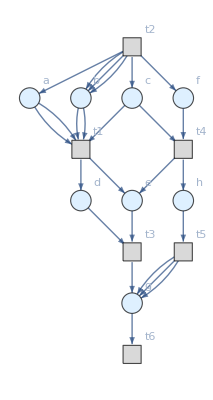
{-Graphics-,{a,b,c,d,e,f,g,h},{t1,t2,t3,t4,t5,t6},{a->t1,a->t1,b->t1,b->t1,c->t1,t1->d,t1->e,t2->a,t2->b,t2->b,t2->b,t2->c,t2->f,d->t3,e->t3,t3->g,c->t4,f->t4,t4->e,t4->h,h->t5,t5->g,t5->g,t5->g,g->t6}}

```mathematica
ClearAll[graph];
graph =petriNetData[<|"States"->{a,b,c,d,e,f,g,h},"Transitions"->{t1,t2,t3,t4,t5,t6}, "Arcs"-> List @@@{a->t1,a->t1,b->t1,b->t1,c->t1,t1->d,t1->e,t2->a,t2->b,t2->b,t2->b,t2->c,t2->f,d->t3,e->t3,t3->g,c->t4,f->t4,t4->e,t4->h,h->t5,t5->g,t5->g,t5->g,g->t6}|>]
```

A Petri net includes places, transitions and arcs. Arcs must go from a place to a transition or vice versa, which makes a Petri net a directed bipartite graph and the nodes represent transitions (events that may occur to cause change in states, marked by square) and places (conditions, marked by circles).

Also we need another thing in Petri net: tokens. The tokens describe the current state in each places, and the number of the tokens determine the firing option to the next state, as we will explain in detail later. Now we can add text-dot to show the tokens and visualize the Petri net as its initial state.

```mathematica
textDot[vertex_, n_, coordinatesDict_]:= Text[StringRepeat["•", n], coordinatesDict[vertex]]
```

```mathematica
buildDotsList[coordinateDict_, vertexWeightDict_, vertices_]:= Module[
	{res = {}},
	Scan[AppendTo[res,textDot[#, vertexWeightDict[#], coordinateDict]]&, vertices];
	res
]
```

```mathematica
petriNetInit[pnet_,init_]:= Module[
	{g, coordinatesDict, vertexWeightDict, graphData, vertexWeight, vertexWeightsDict, epilog},
	g = Graph[First @ pnet, VertexWeight -> Join[Thread[Part[pnet,2] -> init], Thread[Part[pnet,3] -> 0]]];
	graphData = ToExpression @ StringReplace[(ToString[FullForm[g]]), "Graph" -> "List"];
	vertexWeight = Last @ (Last @ graphData[[3]]);
	coordinatesDict = Association @ Thread[graphData[[1]] -> VertexCoordinates /. AbsoluteOptions[g, VertexCoordinates]];
	vertexWeightsDict = Association @ Thread[graphData[[1]] -> vertexWeight];
	epilog = buildDotsList[coordinatesDict, vertexWeightsDict, graphData[[1]]];
	Graph[g, Epilog -> epilog]
]
```

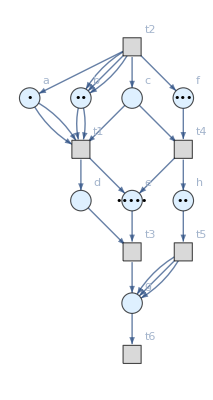

```mathematica
petriNetInit[graph,{1,2,0,0,5,3,0,2}]
```

Now we can clearly see what a Petri net is. These blue circles: a, b, c, d, e, f, g, some with dots(tokens) are places; these gray squares: t1, t2, t3, t4, t5, t6 are transitions; and the edges connected between places and transitions are arcs.

## Codes for Petri net visualization

The next step is to make our Petri net “running”. To do this we need the rules for “firing”. Firing means the tokens from source places with a transition move to source states based on the number of edges between nodes. For example, as the Petri net showed above, place a now has 1 token, and the number of edges between a and t1 is 2, which means place a needs to consume 2 tokens to set up transition t1. The system will randomly select one transition that meets the requirement to fire. For example, if the condition to start transition t1, as t1 has 1 edge to d, and one edge to g, so it will pass 1 token to place d and 1 token to place g. Now we write codes to achieve these firing rules.

petriNetRun[petriNet, initial-tokens, steps]
input: A petriNet and number of tokens in each places, and the steps that the user wants to run.
output: dynamic visualization of how tokens move from state to state in the first n steps.

```mathematica
checkFiring[pnet_, transition_, current_]:= Module[
	{tokenList},
	tokenList = Length@EdgeList[First@pnet, # -> transition] &/@ Part[pnet, 2];
	AllTrue[current - tokenList, NonNegative]
]
```

```mathematica
makeFiring[pnet_, transition_, current_]:= Module[
	{tokenDeleteList,tokenAddList},
	tokenDeleteList = Length@EdgeList[First@pnet, #->transition] &/@ Part[pnet,2];
	tokenAddList = Length@EdgeList[First@pnet, transition->#] &/@ Part[pnet,2];
	current - tokenDeleteList + tokenAddList
]
```

```mathematica
updateFiring[pnet_][current_]:= Module[
	{index},
	index = First @ RandomChoice[Position[checkFiring[pnet, #, current] &/@ pnet[[3]], True]];
	If[IntegerQ[index], 
	makeFiring[pnet, pnet[[3,index]], current], 
	Print["Dead!"]; Abort[]]
]
```

```mathematica
ClearAll[petriNetRun];
petriNetRun[pnet_, init_, step_Integer]:= Module[
	{current = init, g, index},
	current = Nest[updateFiring[pnet], current, step-1];
	index = First @ RandomChoice[Position[checkFiring[pnet, #, current] &/@ pnet[[3]], True]];
	If[IntegerQ[index], 
		makeFiring[pnet, pnet[[3,index]], current], 
		Print["Dead!"]; Abort[]];
	g = petriNetInit[pnet, current];
	HighlightGraph[g, {pnet[[3,index]]}]
]
```

```mathematica
ListAnimate[Table[petriNetRun[graph,{1,2,0,0,5,3,0,2},n],{n,10}],AnimationRate->2]
```

## User interface and animation

A Petri net requires places, transitions, arcs, tokens and firing rules. It requires a lot of input for the users, which is not convenient. To make user input data for a Petri net easier, we are going to create a user interface and the program will translate the input from users to be a PetriNetData structure. Here is the code to start the user interface and helper functions to translate the input to be a Petri net data.

```mathematica
ClearAll[makeMultipleEdges];
makeMultipleEdges[<|"from"->in_,"to"->out_,"numbers"->num_|>]:= Module[{l={}},
	For[i=1,i<=num,i++, AppendTo[l,{in,out}]]; 
	l
]
```

```mathematica
ClearAll[inputTranslator];
inputTranslator[<|"Places" -> placeList_, "Transitions" -> transitionList_, "Arcs" -> arcList_, 
"Initial States"-> <|"e.g: 0,0,1"->init_|>, "Steps"-><|"Input the steps you want to animate"-> steps_|>|>]:=Module[
	{initialState},
	initialState = ToExpression /@ StringSplit[init,","];
	{<|"States"-> First /@ Values /@ placeList, 
	"Transitions"-> First/@ Values /@ transitionList,
	"Arcs"->Join @@ makeMultipleEdges /@ arcList|>, initialState, steps}
]
```

```mathematica
ClearAll[makePetriNetFromInput];
makePetriNetFromInput[input_]:= Module[
	{inputPnetData, initState, steps, pnet},
	{inputPnetData, initState, steps} = inputTranslator[input];
	pnet = petriNet[inputPnetData];
	ListAnimate[Table[petriNetRun[pnet,initState, n],{n, steps}], AnimationRate->1.5]
]
```

```mathematica
ClearAll[PetriNetGeneral];
PetriNetGeneral[]:= FormFunction[<|"Places" -> RepeatingElement[
	CompoundElement[<|"Circles"-> "String"|>]],"Transitions" -> RepeatingElement[CompoundElement[<|"Squares"-> "String"|>]],
	"Arcs" -> RepeatingElement[CompoundElement[<|"from"-> "String","to"-> "String","numbers"-> "Integer"->1|>]],
	"Initial States" -> CompoundElement[{"e.g: 0,0,1"->"String"}],
	"Steps" -> CompoundElement[{"Input the steps you want to animate"-> "Integer"->5}]|>, makePetriNetFromInput][]
```

So when we start the function PetriNetGeneral[], the program will pop out a menu to ask users to input places, transitions, arcs, initial state and steps they want to animate. Below is an example of the user’s interface and the animation after we click “submit” button.

```mathematica
SetDirectory["/Users/luzhiryou/Documents/GitHub/WSS-2019/Final Project"];
Import["GenInterface.jpg"]
```

-Graphics-

```mathematica
PetriNetGeneral[]
```

A more user-friendly might come as future work, but this version will definitely save out time to input data to make and visualize a Petri net.

## Application of Petri net in chemistry

Some papers indicate that Petri nets were first invented in 1939 by Carl Adam Petri for the purpose of describing chemical reactions. To help those interested in chemical reactions, we write another function to visualize the chemical reactions using Petri net.

```mathematica
ClearAll[reduceParentheses];
reduceParentheses[st_String]:= Module[
	{s},
	If[StringPart[st,1] ==="(", s = StringDrop[st,1], s = st];
	If[StringPart[s,-1] ===")", s = StringDrop[s,-1], s];
	s
]
```

```mathematica
getChemicals[st_String]:= First @ StringCases[st, "[" ~~Shortest[c__]~~"]"->c]
```

```mathematica
ClearAll[getStoichiometry];
getStoichiometry[st_String]:=If[StringContainsQ[st,"^"],ToExpression@First@StringCases[st, "^" ~~number__ ->number],1]
```

```mathematica
ClearAll[inputTranslatorHelper];
inputTranslatorHelper[list_List]:= List @@@ Thread[getChemicals/@list-> getStoichiometry/@list]
```

```mathematica
ClearAll[waChemicalReaction];
waChemicalReaction[chemicalReaction_String]:= Module[
	{s,string},
	s = WolframAlpha[chemicalReaction,{{"ReactionKineticsConstant:ChemicalReactionData",1},"ComputableData"}];
	If[s === Missing["NotAvailable"], Print["Missing, try a different notation."]; Abort[],
	s = StringDrop[s, StringLength["K_c  =  "]];
	s = StringSplit[s, "/"];
	s = reduceParentheses/@ s;
	s = StringSplit[s," "];
	string = getChemicals/@Flatten @ s;
	s = inputTranslatorHelper /@ s;
	{s, string}]
]
```

```mathematica
ClearAll[getPlaces];
getPlaces[Chem_List]:= Association /@ Thread["Circles" -> Chem]
```

```mathematica
ClearAll[getTransitions];
getTransitions[{leftChem_List,rightChem_List}] := {<|"Squares"->"T1"|>}
```

```mathematica
ClearAll[getArcs];
getArcs[{leftChems_List, rightChem_List}]:= Module[
	{left, right},
	left = Join @@ Map[{<|"from"-> "T1","to"-> #[[1]],"numbers"-> #[[2]]|>}&, leftChems];
	right = Join @@ Map[{<|"from"-> #[[1]],"to"-> "T1","numbers"-> #[[2]]|>}&, rightChem];
	Join @@ {left, right}
]
```

```mathematica
buildPetriNet[reactions_, chemicals_, init_, steps_]:= Module[
	{places, trans, arcs},
	places = getPlaces[chemicals];
	trans = getTransitions[reactions];
	arcs = getArcs[reactions];
	<|"Places"-> places, "Transitions"->trans, "Arcs"->arcs, "Initial States"-><|"e.g: 0,0,1"->init|>,"Steps"-><|"Input the steps you want to animate"->steps|>|>
]
```

```mathematica
TranslateFromChemToGeneral[<|"Reactions"->{<|"Input the reactions"->st_|>},
	"Initial States"-><|"e.g: 0,0,1"->init_|>,
	"Steps"-><|"Input the steps you want to animate"->steps_|>|>]:= Module[
	{reactants, chemicals,input, inputPnetData, pnet},
	{reactants, chemicals} = waChemicalReaction[st];
	input = buildPetriNet[reactants, chemicals, init, steps];
	makePetriNetFromInput[input]
]
```

```mathematica
ClearAll[PetriNetChemistry];
PetriNetChemistry[]:= FormFunction[<|"Reactions" -> RepeatingElement[CompoundElement[<|"Input the reactions"-> "String"|>]],
	"Initial States" -> CompoundElement[{"e.g: 0,0,1"->"String"}],
	"Steps" -> CompoundElement[{"Input the steps you want to animate"-> "Integer"->5}]|>,TranslateFromChemToGeneral][]
```

Below is an example of visualizing a chemical reaction with input and output.

```mathematica
SetDirectory["/Users/luzhiryou/Documents/GitHub/WSS-2019/Final Project"];
Import["ChemInterface.jpg"]
```

-Graphics-

```mathematica
PetriNetChemistry[]
```

## Further Application of Petri net

Petri net, as a mathematical modeling language, indeed is not limited to visualize chemical processes. In fact, any mathematics model can be somewhat expressed with Petri net.